-(1.54629×10^-13 (635-Energy)^2 Energy^2)/(1-ⅇ^(18/137 √(2/511) √Energy π))

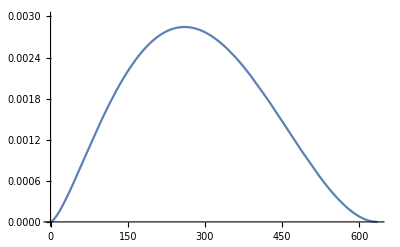

-381.324

```mathematica
Clear["Global`*"]
NdE[Energy_/; Energy>=0 && Energy <= 635.00001]=Normalize[A*(Energy^2*(635-Energy)^2)/(1-Exp[(36*π)/137*√(Energy/(2*511))]), Integrate[#, {Energy, 0, 635.00001}]&]
Plot[NdE[Energy], {Energy, 0, 1600}, PlotRange->{0, .003}]
```

```mathematica
Integrate[((1.8367961863213326*10^-7 )*(0.64-Energy)^2 *Energy^2)/(1-ⅇ^(0.8165943268408818* √Energy)), {Energy, 0, Infinity}]
```

1.02419